# 1. Data Ingestion & Orchestration

```mathematica
(*Automation through terminal and shell script to move CSV file to target folder*)
```

```mathematica
terminal[string_String]:=RunProcess[{"zsh","-i","-c",string}];
Hold[terminal["data_ingest.sh"]];
```

```mathematica
(*

Note on Live Execution:
To run the ingestion automation live,ensure:
1.The data_ingest.sh script is in the terminal's default working directory (typically $HOME).
2.Execution permissions are set (chmod+x data_ingest.sh).
3.Valid CSV in ~/Downloads
4.The Hold[] wrapper is removed from the command above.

Demo Mode (Default):If dependencies are missing,the system automatically falls back to embedded Sample Data to demonstrate the visualization logic without configuration.

*)
```

# 2. Data Transformation & Validation

## Data & Sample

```mathematica
(*Define the live path*)
livePath=StringJoin[$HomeDirectory,"/Documents/HealthData/raw_data.csv"]
```

/Users/andrefreitas/Documents/HealthData/raw_data.csv

```mathematica
(*Import the data*)
```

```mathematica
(*The Logic:Try to find the file,otherwise load sample to run in DEMO mode*)data=If[FileExistsQ[livePath],Import[livePath,"RawData"],(*ELSE:Print a message and use sample*)Print["⚠️ Live file not found. Switching to DEMO MODE with sample data."];];
```

⚠️ Live file not found. Switching to DEMO MODE with sample data.

```mathematica
(*Small sample of the data filtered by type "sleep"*)
```

```mathematica
{First[data],Select[data,Function[#[[1]]==="Sleep"]][[1;;3]]}//TableForm;
```

## Variables1

```mathematica
(*Putting data into Tabular format, filtering for Sleep and selecting only the relevant columns (first 4)*)
```

```mathematica
sleepTabular1=Tabular[Select[data,Function[#[[1]]==="Sleep"]],First[data]][[All,1;;4]]
```

```mathematica
(*adding a column 'Date' to indicate the day in which the sleeping started*)
```

```mathematica
sleepTabular2=TransformColumns[sleepTabular1,{"Type","Date"->Function[StringSplit[#Start," "]/.{a_,b_}->a]}]
```

```mathematica
(*Variable that list all days in string ISODate format from when sleeping data started to be collected (17/05/2025) up to the current day*)
```

```mathematica
dates=(DateString[#,"ISODate"]&/@DateRange[DateObject["2025-05-17"],Today,"Day"]);
```

## Functions

```mathematica
(*Function that adds column "Duration2" and "Time Range" which gives the duration of each sleeping session restricted to a specific day*)
```

```mathematica
f[date_String]:=TransformColumns[Select[sleepTabular2,Function[(StringSplit[#End," "]/.{a_,b_}->a)==date||#Date==date]],{"Duration2"->Function[If[(StringSplit[#End," "]/.{a_,b_}->a)!=date,DateObject[StringJoin[date," 23:59"]]-DateObject[#Start],If[(StringSplit[#Start," "]/.{a_,b_}->a)!=date,DateObject[#End]-DateObject[StringJoin[date," 00:01"]],DateObject[#End]-DateObject[#Start]],DateObject[#End]-DateObject[#Start]]],"TimeRange"->Function[If[(StringSplit[#End," "]/.{a_,b_}->a)!=date,(StringSplit[#Start," "]/.{a_,b_}->b)<>"-23:59",If[(StringSplit[#Start," "]/.{a_,b_}->a)!=date,"00:00-"<>(StringSplit[#End," "]/.{a_,b_}->b),(StringSplit[#Start," "]/.{a_,b_}->b)<>"-"<>(StringSplit[#End," "]/.{a_,b_}->b)]]]}]
```

```mathematica
(*example: the column "duration2" displays the amount of sleep only up until 23:59 on the 21/05/2025*)
```

```mathematica
f["2025-05-21"]
```

```mathematica
(*testing I can use the function to calculate total amount of sleep from 00:00 to 23:59 on any given day*)
```

```mathematica
f["2025-05-21"][[All,"Duration2"]]//Normal//Total
```

932 min

```mathematica
(*Function Gives the total amount of sleep for the inputed day, includint partial days*)
```

```mathematica
totalDaySleep[date_String]:=(f[date][[All,6]]//Normal//Total)/.Quantity[x_,"Minutes"]->Quantity[MixedMagnitude[{0,x}],MixedUnit[{"Hours","Minutes"}]]
```

```mathematica
(*Example*)
```

```mathematica
totalDaySleep["2026-01-25"]
```

14 33

```mathematica
(*Function gives last x days (including current day) as string "ISODate"*)
```

```mathematica
listOfDates[daysback_Integer]:=(DateString[#,"ISODate"]&/@DateRange[DatePlus[Today,-daysback],Yesterday,"Day"])
```

```mathematica
(*Example*)
```

```mathematica
listOfDates[7]
```

{2026-01-24,2026-01-25,2026-01-26,2026-01-27,2026-01-28,2026-01-29,2026-01-30}

```mathematica
(*Function Gives the total amount of sleep per day in the last "daysback"s not including current day*)
```

```mathematica
totalDaySleep2[daysback_Integer]:=Rule@@@Partition[Riffle[listOfDates[daysback],Map[totalDaySleep[#]&,listOfDates[daysback]]],2]
```

```mathematica
(*Example*)
```

```mathematica
totalDaySleep2[3]
```

{2026-01-28→14 36,2026-01-29→13 27,2026-01-30→14 2}

## Variables 2

Defining secondary feature set based on the primary variables established in Variables 1 subsection and on the functions established in the Functions section.

```mathematica
(*All data on total sleep (in hours and minutes) per day as an ASSOCIATION*)
```

```mathematica
sleepData=Rule@@@Partition[Riffle[dates,Map[totalDaySleep,dates]],2];
```

```mathematica
(*All data on total sleep per day as list of decimal hours*)
```

```mathematica
sleepData2=Drop[Function[UnitConvert[#,"Hours"]]/@Values[sleepData],-1]//N;
```

# Insights & Visual Monitoring

## Total Hours per day

```mathematica
(*Function to manually calculate the total amount of sleep in a day, for partial days calculations*)
```

```mathematica
manualSleeping[hours_List,minutes_List]:=Quantity[MixedMagnitude[{Total[Join[hours,{IntegerPart[Total[minutes]/60]}]],FractionalPart[Total[minutes]/60]*60}],MixedUnit[{"Hours","Minutes"}]]
```

```mathematica
(*Example*)
```

```mathematica
(*2026-01-31*)
```

```mathematica
manualSleeping[{1,4},{23,34}]
```

5 57

```mathematica
(*Total sleep in current day - Almost always partial*)
```

```mathematica
totalDaySleep[DateString[Today,"ISODate"]]
```

7 26

```mathematica
(*Total sleep per day from the last 8 days*)
```

```mathematica
totalDaySleep2[7]
```

{2026-01-24→14 6,2026-01-25→14 33,2026-01-26→13 46,2026-01-27→14 0,2026-01-28→14 36,2026-01-29→13 27,2026-01-30→14 2}

```mathematica
(*Avarege sleep from the last 7 days*)
```

```mathematica
((Mean[
UnitConvert[#,"Minutes"]&/@
([[All,2]])]
//N)
/60.0)/.Quantity[a_,"Minutes"]:>Quantity[MixedMagnitude[{IntegerPart[a],IntegerPart[FractionalPart[a]*60]}],MixedUnit[{"Hours","Minutes"}]]
```

14 4

## Naps per day

```mathematica
(*tracking the number of naps (under 120 min) per day*)
```

```mathematica
Function[Length[Select[f[#],Function[#Duration2<120]]]]/@dates
```

{8,8,15,11,8,9,5,8,10,10,7,8,9,10,11,9,6,11,11,12,9,8,8,13,8,10,12,8,8,8,9,8,7,8,5,9,9,6,6,11,8,7,8,8,7,4,6,10,6,5,8,5,5,6,6,5,6,6,6,5,6,4,6,5,4,6,5,2,5,5,5,3,5,5,6,5,7,2,8,7,4,2,4,4,4,5,4,4,3,6,3,6,3,4,5,4,5,6,4,6,3,3,4,3,3,4,5,4,6,4,3,4,4,7,5,4,6,5,3,5,5,5,5,5,7,3,5,3,5,5,4,3,1,4,5,5,5,4,5,3,4,4,3,4,4,4,3,3,3,5,6,8,4,4,3,4,4,7,3,4,3,5,4,4,4,3,4,2,3,5,3,4,5,3,3,5,5,4,3,3,4,4,4,4,3,5,5,4,3,3,4,3,4,4,5,4,3,5,5,3,7,8,5,5,3,4,3,4,5,4,3,5,3,4,3,6,3,4,4,3,3,4,3,3,3,5,4,4,4,5,5,1,3,2,3,3,2,3,3,4,3,3,3,2,3,3,3,2,4,2,2,2,4,2,2,2,2,4,2,0}

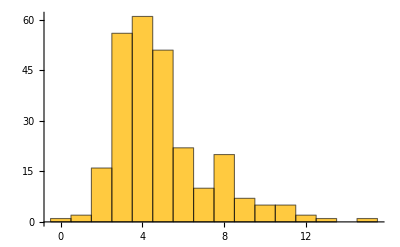

```mathematica
Histogram[]
```

## Distribution of Naps along specific days

```mathematica
barChartSleep[date_String]:=BarChart[f[date][[All,"Duration2"]]//QuantityMagnitude//Normal//Reverse,ChartLabels->(f[date][[All,"TimeRange"]]//Normal//Reverse)]
```

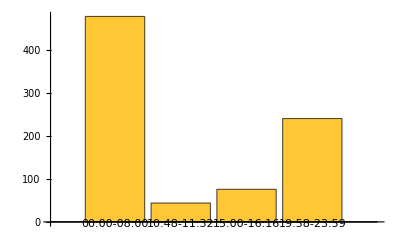
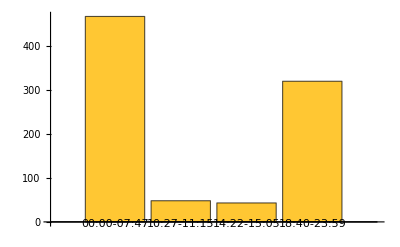
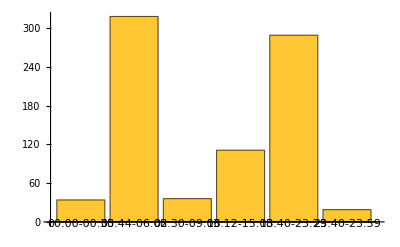
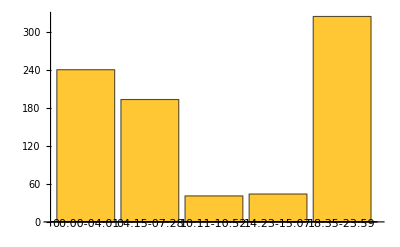

```mathematica
barChartSleep[#]&/@listOfDates[4]
```

## Moving average total hours per day

```mathematica
(*Moving average for 7 days agains raw data*)
```

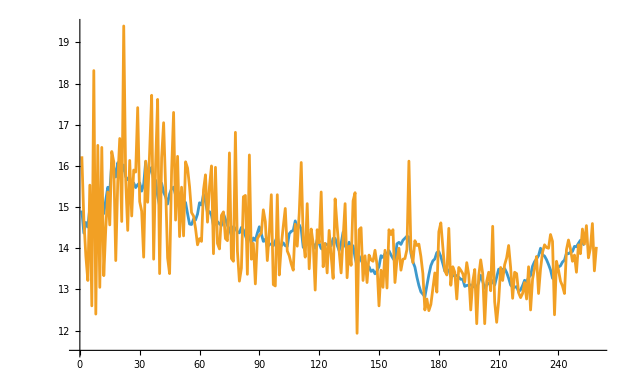

```mathematica
ListLinePlot[{MovingAverage[sleepData2,7],sleepData2}]
```

```mathematica
(*Moving average only*)
```

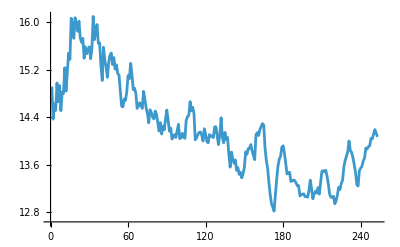

```mathematica
ListLinePlot[MovingAverage[sleepData2,7]]
```

```mathematica
(*Fitting the data with ListFitPlot[]*)
```

```mathematica
ListFitPlot[sleepData2[[1;;-2]],PlotRange->{Automatic,{12,20}}]
```

-Graphics-